## Coherent Information - EPR Qudit - Poisson/Gaussian Noise Model

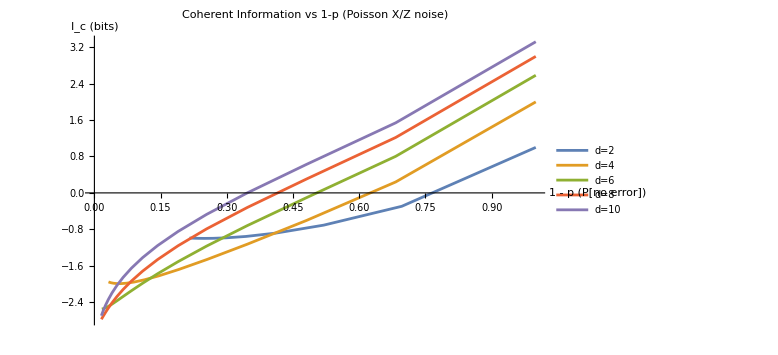

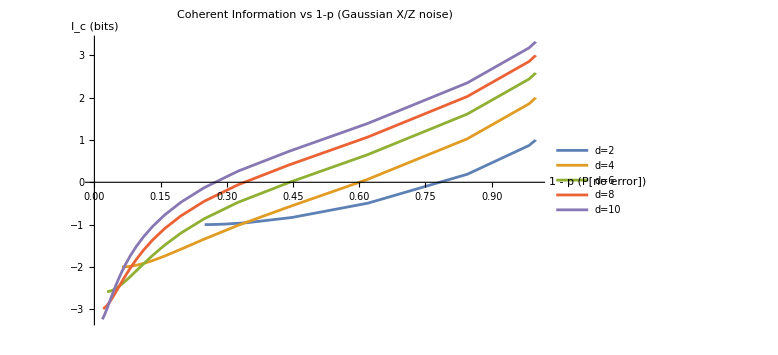

```mathematica
ClearAll[XOperator, ZOperator, VonNeumannEntropyBits];


(* Define qudit X, Z operators and von Neumann entropy in bits ________________ *)
(* Generalized Pauli X on a qudit of dimension d *)
XOperator[d_Integer] := SparseArray[
   Table[
     {Mod[i, d] + 1, i} -> 1,
     {i, 1, d}
   ],
   {d, d}
];

(* Generalized Pauli Z on a qudit of dimension d *)
ZOperator[d_Integer] := DiagonalMatrix[
   Table[Exp[2 Pi I (k - 1)/d], {k, 1, d}]
];

(* Von Neumann entropy in bits, with some numerical hygiene *)
VonNeumannEntropyBits[rho_?MatrixQ] := Module[{rh, evals},
  (* enforce Hermiticity, chop tiny imaginary parts *)
  rh = Chop[(rho + ConjugateTranspose[rho])/2];
  evals = Chop[Eigenvalues[rh]];
  evals = Select[evals, # > 10^-12 &]; (* discard 0 or negative junk *)
  -Total[evals Log2[evals]]
];
ClearAll[PoissonDistributionZ];


(* Symmetric Poisson distribution on Z_d, folded modulo d and normalized ________________ *)
(* Poisson-like distribution on Z_d with parameter λ
   cutoff controls how many integers n we include in the sum *)
PoissonDistributionZ[d_Integer, λ_?NumericQ, cutoff_Integer : 15] :=
 Module[{nRange, w, probs},
  nRange = Range[-cutoff, cutoff];

  (* careful definition to avoid 0.^0 when λ = 0 and n = 0 *)
  w[n_] := Which[
    PossibleZeroQ[λ] && n == 0, 1.,            (* exactly no noise *)
    PossibleZeroQ[λ] && n != 0, 0.,
    True, Exp[-2 λ] (λ^Abs[n]/Factorial[Abs[n]])
  ];

  probs = ConstantArray[0., d];
  Do[
    probs[[Mod[n, d] + 1]] += w[n],
    {n, nRange}
  ];
  probs/Total[probs]
];
ClearAll[GaussianDistributionZ];


(* Symmetric discrete Gaussian on Z_d with cutoff and normalization ________________ *)
(* Gaussian-like distribution on Z_d with std deviation σ
   cutoffFactor * σ sets how far in n we sum *)
GaussianDistributionZ[d_Integer, σ_?NumericQ, cutoffFactor_: 4] :=
 Module[{cutoff, nRange, w, probs},
  cutoff = Max[1, Ceiling[cutoffFactor σ]];
  nRange = Range[-cutoff, cutoff];
  w[n_] := Exp[-n^2/(2 σ^2)];
  probs = ConstantArray[0., d];
  Do[
    probs[[Mod[n, d] + 1]] += w[n],
    {n, nRange}
  ];
  probs/Total[probs]
];
ClearAll[CoherentInformationEPR];


(* Compute coherent information for the noise channels ________________ *)
CoherentInformationEPR[d_Integer, px_List, pz_List] :=
 Module[{X, Z, xPowers, zPowers, kraus, rhoQ0, rhoQ, psi, rhoRQ0, rhoRQ,
   SQ, SRQ},

  (* sanity checks *)
  If[Length[px] =!= d || Length[pz] =!= d,
   Return[$Failed, Module]
  ];

  X = XOperator[d];
  Z = ZOperator[d];

  xPowers = Table[MatrixPower[X, n], {n, 0, d - 1}];
  zPowers = Table[MatrixPower[Z, m], {m, 0, d - 1}];

  (* Kraus operators: K_{n,m} = sqrt(Px(n) Pz(m)) X^n Z^m *)
  kraus = Flatten[
    Table[
      Sqrt[px[[n + 1]] pz[[m + 1]]] xPowers[[n + 1]].zPowers[[m + 1]],
      {n, 0, d - 1}, {m, 0, d - 1}
    ],
    1
  ];

  (* single-qudit maximally mixed state *)
  rhoQ0 = IdentityMatrix[d]/d;

  rhoQ = Total[(# . rhoQ0 . ConjugateTranspose[#]) & /@ kraus];

  (* maximally entangled state |Ψ_d> as a vector in d^2-dim space *)
  psi = 1/Sqrt[d] Flatten[IdentityMatrix[d]];
  rhoRQ0 = Outer[Times, psi, Conjugate[psi]];

  rhoRQ = Total[
    With[{K = KroneckerProduct[IdentityMatrix[d], #]},
       K . rhoRQ0 . ConjugateTranspose[K]
     ] & /@ kraus
  ];

  SQ = VonNeumannEntropyBits[rhoQ];
  SRQ = VonNeumannEntropyBits[rhoRQ];

  SQ - SRQ
];


(* dimensions to study *)
dList = {2, 4, 6, 8, 10};


(* noise strength grid for Poisson *)
lambdaList = Range[0., 1.5, 0.1];
(* Evaluate Ic vs (1-p) for Poisson X/Z noise across different d ________________ *)
poissonData =
  Table[
    Module[{px, pz, Ic, q},
      Table[
        px = PoissonDistributionZ[d, λ, 15];
        pz = px; (* same distribution for X and Z *)
        q = px[[1]] pz[[1]]; (* prob of no X and no Z error *)
        Ic = CoherentInformationEPR[d, px, pz];
        {q, Ic}
        ,
        {λ, lambdaList}
      ] // SortBy[#, First] & (* sort by q = 1-p *)
    ],
    {d, dList}
  ];


(* Plot coherent information curves for Poisson noise ________________ *)
poissonPlot = ListLinePlot[
  poissonData,
  PlotLegends -> (("d=" <> ToString[#]) & /@ dList),
  AxesLabel -> {"1 - p (P[no error])", "I_c (bits)"},
  PlotLabel -> "Coherent Information vs 1-p (Poisson X/Z noise)",
  PlotRange -> All,
  ImageSize -> Large
];

poissonPlot


(* noise strength grid for Gaussian *)
sigmaList = Range[0.1, 3., 0.1];
(* Evaluate Ic vs (1-p) for Gaussian X/Z noise across different d ________________ *)
gaussianData =
  Table[
    Module[{px, pz, Ic, q},
      Table[
        px = GaussianDistributionZ[d, σ, 4];
        pz = px;
        q = px[[1]] pz[[1]]; (* prob of no error in X and Z *)
        Ic = CoherentInformationEPR[d, px, pz];
        {q, Ic}
        ,
        {σ, sigmaList}
      ] // SortBy[#, First] &
    ],
    {d, dList}
  ];
  
  
(* Plot coherent information curves for Gaussian noise ________________ *)
gaussianPlot = ListLinePlot[
  gaussianData,
  PlotLegends -> (("d=" <> ToString[#]) & /@ dList),
  AxesLabel -> {"1 - p (P[no error])", "I_c (bits)"},
  PlotLabel -> "Coherent Information vs 1-p (Gaussian X/Z noise)",
  PlotRange -> All,
  ImageSize -> Large
];

gaussianPlot
```

```mathematica
(* Check normalization of Poisson kernel *)
CheckPoissonNorm[d_, λ_, cutoff_:15] := Total[PoissonDistributionZ[d, λ, cutoff]]

(* Check normalization of Gaussian kernel *)
CheckGaussianNorm[d_, σ_, cutoffFactor_:4] := Total[GaussianDistributionZ[d, σ, cutoffFactor]]

(* Print normalization for sample values *)
Table[
  {
    "d" -> d,
    "λ" -> λ,
    "PoissonNorm" -> N[CheckPoissonNorm[d, λ]],
    "σ" -> σ,
    "GaussianNorm" -> N[CheckGaussianNorm[d, σ]]
  },
  {d, {2, 6, 10}},
  {λ, {0, 0.5, 1.5}},
  {σ, {0.1, 0.5, 3}}
] // Flatten
```

{d→2,λ→0,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→2,λ→0,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→2,λ→0,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→2,λ→0.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→2,λ→0.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→2,λ→0.5,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→2,λ→1.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→2,λ→1.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→2,λ→1.5,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→6,λ→0,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→6,λ→0,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→6,λ→0,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→6,λ→0.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→6,λ→0.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→6,λ→0.5,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→6,λ→1.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→6,λ→1.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→6,λ→1.5,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→10,λ→0,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→10,λ→0,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→10,λ→0,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→10,λ→0.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→10,λ→0.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→10,λ→0.5,PoissonNorm→1.,σ→3,GaussianNorm→1.,d→10,λ→1.5,PoissonNorm→1.,σ→0.1,GaussianNorm→1.,d→10,λ→1.5,PoissonNorm→1.,σ→0.5,GaussianNorm→1.,d→10,λ→1.5,PoissonNorm→1.,σ→3,GaussianNorm→1.}